## Release Notes

challenge1-4 : Explore correlations...
challenge1-3 : Try the full case - wow, did this fail!
challenge1-2 : Add in a constant term to the fits. 
challenge1-1 : Periodogram to find periods (PMC.m extended to eliminate dead Gaussians)

## Setup

```mathematica
(* Initialize stuff *)
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
Needs["PMC`"];
Needs["GLSTools`"];
```

```mathematica
(* Read in data *)
vrad =SemanticImport["vrad_simu_challenge_inclination_90_1.rdb",ExcludedLines->{2}];
```

```mathematica
Keys[vrad][[1]]//Normal
```

{jdb,rv,sig_rv,fwhm,sig_fwhm,bis_span,sig_bis_span,rhk,sig_rhk,rv_osc_and_gran,rv_activity,rv_planet,rv_inst_noise,fwhm_osc_and_gran,fwhm_activity,fwhm_inst_noise,bis_span_osc_and_gran,bis_span_activity,bis_span_inst_noise,rhk_osc_and_gran,rhk_activity,rhk_inst_noise}

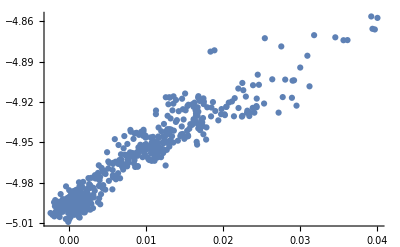

```mathematica
ListPlot@Transpose[Normal@vrad[All,#1]&/@{#rv+0.0085&,#rhk&}]
```

```mathematica
Min[vrad[[All,"rhk"]]]
```

-5.00924

```mathematica
vrad[All,#]&/@ {#"rv"-#"rv_planet"}&
```

```mathematica
Normal@vrad[All,#1]&/@{#rv-#"rv_planet"-#"rv_activity"-#"rv_osc_and_gran"-#"rv_inst_noise"&}
```

{{-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008505,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008503,-0.008504,-0.008503,-0.008505,-0.008504,-0.008505,-0.008504,-0.008504,-0.008504,-0.008504,-0.008505,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008503,-0.008504,-0.008505,-0.008505,-0.008504,-0.008504,-0.008505,-0.008504,-0.008505,-0.008505,-0.008504,-0.008505,-0.008505,-0.008505,-0.008505,-0.008504,-0.008504,-0.008503,-0.008505,-0.008505,-0.008504,-0.008504,-0.008505,-0.008504,-0.008504,-0.008505,-0.008504,-0.008505,-0.008503,-0.008505,-0.008503,-0.008504,-0.008505,-0.008505,-0.008504,-0.008504,-0.008503,-0.008504,-0.008505,-0.008503,-0.008505,-0.008504,-0.008504,-0.008504,-0.008505,-0.008504,-0.008504,-0.008504,-0.008505,-0.008504,-0.008504,-0.008505,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008505,-0.008503,-0.008504,-0.008505,-0.008504,-0.008504,-0.008504,-0.008504,-0.008503,-0.008504,-0.008503,-0.008503,-0.008504,-0.008504,-0.008504,-0.008505,-0.008504,-0.008505,-0.008504,-0.008504,-0.008505,-0.008504,-0.008503,-0.008504,-0.008504,-0.008504,-0.008504,-0.008505,-0.008504,-0.008504,-0.008505,-0.008505,-0.008504,-0.008504,-0.008503,-0.008504,-0.008505,-0.008505,-0.008504,-0.008504,-0.008504,-0.008504,-0.008503,-0.008504,-0.008504,-0.008504,-0.008505,-0.008504,-0.008504,-0.008505,-0.008505,-0.008503,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008503,-0.008504,-0.008503,-0.008504,-0.008504,-0.008503,-0.008505,-0.008504,-0.008504,-0.008504,-0.008505,-0.008504,-0.008503,-0.008504,-0.008505,-0.008504,-0.008504,-0.008503,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008505,-0.008504,-0.008503,-0.008504,-0.008504,-0.008504,-0.008505,-0.008504,-0.008504,-0.008503,-0.008504,-0.008504,-0.008504,-0.008505,-0.008503,-0.008504,-0.008504,-0.008504,-0.008505,-0.008505,-0.008503,-0.008504,-0.008504,-0.008503,-0.008505,-0.008504,-0.008503,-0.008505,-0.008503,-0.008504,-0.008505,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008505,-0.008504,-0.008504,-0.008504,-0.008504,-0.008503,-0.008504,-0.008504,-0.008503,-0.008504,-0.008505,-0.008504,-0.008503,-0.008504,-0.008504,-0.008504,-0.008505,-0.008504,-0.008505,-0.008504,-0.008505,-0.008504,-0.008505,-0.008503,-0.008503,-0.008505,-0.008504,-0.008504,-0.008504,-0.008503,-0.008504,-0.008505,-0.008504,-0.008504,-0.008504,-0.008505,-0.008505,-0.008503,-0.008504,-0.008504,-0.008505,-0.008504,-0.008505,-0.008505,-0.008504,-0.008503,-0.008504,-0.008505,-0.008504,-0.008504,-0.008505,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008503,-0.008504,-0.008504,-0.008505,-0.008505,-0.008504,-0.008505,-0.008505,-0.008505,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008503,-0.008503,-0.008504,-0.008503,-0.008503,-0.008504,-0.008504,-0.008504,-0.008505,-0.008503,-0.008505,-0.008504,-0.008504,-0.008505,-0.008503,-0.008503,-0.008504,-0.008504,-0.008504,-0.008504,-0.008505,-0.008504,-0.008504,-0.008504,-0.008505,-0.008505,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008505,-0.008504,-0.008505,-0.008503,-0.008504,-0.008505,-0.008504,-0.008504,-0.008505,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008503,-0.008505,-0.008504,-0.008505,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008505,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008503,-0.008504,-0.008504,-0.008504,-0.008504,-0.008503,-0.008504,-0.008504,-0.008504,-0.008505,-0.008504,-0.008504,-0.008504,-0.008505,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008503,-0.008504,-0.008504,-0.008504,-0.008504,-0.008503,-0.008505,-0.008504,-0.008503,-0.008504,-0.008503,-0.008505,-0.008504,-0.008504,-0.008504,-0.008505,-0.008503,-0.008504,-0.008504,-0.008504,-0.008503,-0.008503,-0.008504,-0.008504,-0.008504,-0.008503,-0.008504,-0.008504,-0.008505,-0.008505,-0.008505,-0.008504,-0.008505,-0.008503,-0.008504,-0.008503,-0.008504,-0.008504,-0.008504,-0.008505,-0.008504,-0.008505,-0.008504,-0.008503,-0.008505,-0.008504,-0.008503,-0.008504,-0.008503,-0.008505,-0.008504,-0.008505,-0.008505,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008503,-0.008503,-0.008504,-0.008504,-0.008505,-0.008505,-0.008505,-0.008504,-0.008504,-0.008504,-0.008504,-0.008505,-0.008505,-0.008503,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008505,-0.008504,-0.008503,-0.008505,-0.008503,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008505,-0.008504,-0.008505,-0.008504,-0.008504,-0.008504,-0.008504,-0.008505,-0.008504,-0.008504,-0.008505,-0.008504,-0.008504,-0.008504,-0.008504,-0.008504,-0.008505,-0.008505,-0.008504,-0.008504,-0.008503,-0.008504,-0.008505,-0.008505,-0.008505,-0.008504,-0.008505,-0.008505,-0.008504,-0.008504,-0.008503,-0.008504}}